```mathematica
Clear["Global`*"]
mesh[x1_,x2_,hx_,y1_,y2_,hy_]:=Module[{},Table[{x,y},{x,x1,x2,hx},{y,y1,y2,hy}]]
mesh::usage="Build the matrix in the given rectangular area"
randomWalk[x1_,x2_,hx_,y1_,y2_,hy_,n_]:=Block[{a,numx,numy,x,y,lenx,leny,maxx,maxy,i,b={},rand},a=mesh[x1,x2,hx,y1,y2,hy];lenx=Length[a];leny=Length[a[[1]]];
maxx=a[[lenx]][[1]][[1]];maxy=a[[1]][[leny]][[2]];numx=RandomInteger[{1,lenx}];numy=RandomInteger[{1,leny}];{x,y}=a[[numx]][[numy]];AppendTo[b,{x,y}];For[i=0,i<n,AppendTo[b,{x,y}];i++,
Which[
(*Point at the corner*)
{x,y}=={x1,maxy},rand=RandomInteger[1];Which[rand==0,numx++,rand==1,numy--],{x,y}=={x1,y1},rand=RandomInteger[1];Which[rand==0,numx++,rand==1,numy++],{x,y}=={maxx,y1},rand=RandomInteger[1];Which[rand==0,numx--,rand==1,numy++],{x,y}=={maxx,maxy},rand=RandomInteger[1];Which[rand==0,numx--,rand==1,numy--],
(*Point on four sides*)
x==x1,rand=RandomInteger[2];Which[rand==0,numx++,rand==1,numy++,rand==2,numy--],x==maxx,rand=RandomInteger[2];Which[rand==0,numx--,rand==1,numy++,rand==2,numy--],y==y1,rand=RandomInteger[2];Which[rand==0,numy++,rand==1,numx++,rand==2,numx--],y==maxy,rand=RandomInteger[2];Which[rand==0,numy--,rand==1,numx++,rand==2,numx--],
(*Point inside*)
True,rand=RandomInteger[3];Which[rand==0,numx--,rand==1,numx++,rand==2,numy--,rand==3,numy++]
];{x,y}=a[[numx]][[numy]]
];Show[{ListLinePlot[b,Mesh->Full],Graphics[Text["Start",b[[1]]]],Graphics[{PointSize[Large],Point[b[[1]]]}]}]]
randomWalk::usage="random walk starting at a random point, the last argument is the number of steps to go"
```

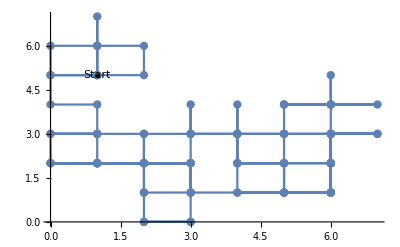

```mathematica
randomWalk[0,10,1,0,10,1,100]
```